# Inflation S.M. Boucenna. v0,10

```mathematica
Quit[]
```

## > Startup

```mathematica
AppendTo[$Path, ToFileName[{$HomeDirectory,"Dropbox","physics","projects","1.mate"}]];
PacletDirectoryAdd[ToFileName[{$HomeDirectory,"Dropbox","physics","projects","1.mate"}]];
<<Pitch`
```

************************************************ PITCH ************************************************Sofiane Boucenna
Version: 0.57*******************************************************************************************************

Loading susyno...

XXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX  XXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXVersion: 3.5; Author: Renato Fonseca.
For help, use the built-in  and associated documentation pages.A tutorial exclusively dedicated to the group theory functionalities of the program can be found .XXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX

Loading Pitch...

Done.

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

## > General Non-minimal + CW general expressions

```mathematica
fa=10^12/Mpl GeV ; (*no effect unless ~ 10^17*)

(*EXP data*)
(*Planck_2015_Results_XX_Constraints_inflation - table 3, k*=0.05*)
ΔR2EXP=2.196 10^-9;(*Nobu's: 2.215 10^-9;*) 
nsExp 68min=0.9655-0.0062;
nsExp 68max=0.9655+0.0062;
rExp max=0.1;
```

```mathematica
dσ[ϕ_,ξ_]:=(√(1+(6ξ+1)ξ ϕ^2))/(1+ξ ϕ^2);
VJordanFull[ϕ_,ξ_,V0_,λ_]:=(λ/4 (ϕ^2- fa^2)^2+V0)(Mpl GeV)^4; 
 VEinsteinFull[ϕ_,ξ_,V0_,λ_]:=(λ/4(ϕ^2- fa^2)^2+V0)/((1+ξ ϕ^2)^2)(Mpl GeV)^4;
V[ϕ_,ξ_,V0_]:=(1/4(ϕ^2- fa^2)^2+0 V0)/((1+ξ ϕ^2)^2); (*WARNING: Check normalization of λ from potential. Note that λ is a multiplicative factor appearing in ΔR2. To get the scale of this potential, use  VEinsteinFull*)
```

```mathematica
ϵ[ϕ_,ξ_,V0_]:= 1/2(D[V[Φ,ξ,V0],Φ]/(V[Φ,ξ,V0]dσ[Φ,ξ]))^2/.Φ->ϕ

η[ϕ_,ξ_,V0_]:=(D[V[Φ,ξ,V0],{Φ,2}]/V[Φ,ξ,V0] dσ[Φ,ξ]^-2-(D[V[Φ,ξ,V0],Φ]D[dσ[Φ,ξ],Φ])/(V[Φ,ξ,V0] dσ[Φ,ξ]^3))/.Φ->ϕ
ζ2[ϕ_,ξ_,V0_]:=(D[V[Φ,ξ,V0],Φ]/(V[Φ,ξ,V0]dσ[Φ,ξ]))(D[V[Φ,ξ,V0],{Φ,3}]/(V[Φ,ξ,V0] dσ[Φ,ξ]^3)-3(D[V[Φ,ξ,V0],{Φ,2}]D[dσ[Φ,ξ],Φ])/(V[Φ,ξ,V0] dσ[Φ,ξ]^4)+3(D[V[Φ,ξ,V0],Φ] D[dσ[Φ,ξ],Φ]^2)/(V[Φ,ξ,V0] dσ[Φ,ξ]^5)-(D[V[Φ,ξ,V0],Φ]D[dσ[Φ,ξ],{Φ,2}])/(V[Φ,ξ,V0] dσ[Φ,ξ]^4) )/.Φ->ϕ
```

```mathematica
Hinflation[ϕ_,ξ_,V0_,λ_]:=(√VEinsteinFull[ϕ,ξ,V0,λ])/(√3 Mpl GeV)


ΔR2[ϕ_,λ_,ξ_,V0_]:=λ/(24 π^2 ϵ[ϕ,ξ,V0])V[ϕ,ξ,V0];


efolds[ξ_,fe_,fk_,V0_]:=1/(√2)Quiet[NIntegrate[1/(√ϵ[ϕ,ξ,V0])dσ[ϕ,ξ],{ϕ,fe,fk}]];

ns[ϕ_,ξ_,V0_]:=1-6 ϵ[ϕ,ξ,V0]+ 2 η[ϕ,ξ,V0];
r[ϕ_,ξ_,V0_]:=16 ϵ[ϕ,ξ,V0];
α[ϕ_,ξ_,V0_]:=16 ϵ[ϕ,ξ,V0] η[ϕ,ξ,V0]-24 ϵ[ϕ,ξ,V0]^2-2ζ2[ϕ,ξ,V0];
α2[ϕ_,ξ_,V0_]:=16 ϵ[ϕ,ξ,V0] η[ϕ,ξ,V0]-24 ϵ[ϕ,ξ,V0]^2;
```

## > Non-minimal coupling routine

```mathematica
inflate[ξ_,Nfolds_,VERBOSE_:False]:=Module[{ϕe,ϕ0,fk2,feϵ,feη,feζ,λA,ϕmin,c,V0sol,Φ},

ϕmin=Quiet[FindRoot[(D[V[Φ,ξ,0.],Φ]/.Φ->f)==0.,{f,1}][[1,2]]];
V0sol=0.;

feϵ=Quiet[NSolve[{ϵ[f,ξ,0]==1.,f∈ Reals,f>0},f]][[-1,1,2]];
feη=Quiet[NSolve[{Abs[η[f,ξ,0]]==1.,f∈ Reals,f>0},f]][[-1,1,2]];
feζ=Quiet[NSolve[{ζ2[f,ξ,0]==1.,f∈ Reals,f>0},f]][[-1,1,2]];

ϕe=Max[feϵ,feη,feζ];

If[ϵ[ϕe,ξ,V0sol]<1.01 && ϵ[ϕe,ξ,V0sol]>0.99&&  ϕe>0.,,ϕe==ⅈ];
 
If[Im[ϕe]==0.,
	For[c=1.01,c<10.,c+=1.,
           ϕ0=Quiet[FindRoot[efolds[ξ,ϕe,ϕ0sol,V0sol]==Nfolds,{ϕ0sol,ϕe *c}]][[1,2]];
           If[efolds[ξ,ϕe,ϕ0,V0sol]/Nfolds<1.01,Break[]];
	];
	If[Im[ϕ0]≠0||ϕ0<0|| efolds[ξ,ϕe,ϕ0,V0sol]/Nfolds>1.001,ϕ0=0];
,
	ϕ0=0
];



If[ϕ0≠0,λA=Quiet[FindRoot[ΔR2[ϕ0,λ,ξ,V0sol]==ΔR2EXP,{λ,10^-8}][[1,2]]],λA=0];


If [VERBOSE,

Print[" Minimum during inflation=",ϕmin, " | V0=",V0sol];

Print["\n N=", efolds[ξ,ϕe,ϕ0,V0sol]//Chop];
Print[
"\n The fields rolls from ϕi=",ϕ0//Chop," (Hi=",Hinflation[ϕ0,ξ,V0sol,λA]//Chop, ")",
" to ϕe=",ϕe//Chop," (He=",Hinflation[ϕe,ξ,V0sol,λA]//Chop,")"];

Print["\n Potential at start of inflation [GeV]: ",VEinsteinFull[ϕ0,ξ,V0sol,λA]^(1/4)," (Einstein) | ", VJordanFull[ϕ0,ξ,V0sol,λA]^(1/4), " (Jordan)"];
Print["\n Required Quartic coupling: λA=",λA, " (Log[λA]=",Log[10,λA],")"];

];


Return[{ϕ0,V0sol,λA,ns[ϕ0,ξ,V0sol  ],r[ϕ0,ξ,V0sol ],10^4 α[ϕ0,ξ,V0sol  ]}];

]
```

```mathematica
fa=0.0001 ;
ξbench=100;
sol=inflate[ξbench,50.,True];

Print["ns  = ",sol[[4]]," | rs = ",sol[[5]]," | 10^4α = ",sol[[6]] ];
nsExp 68min≤ sol[[4]]≤ nsExp 68max
```

Minimum during inflation=6.52763×10^6 | V0=0.

N=50.

The fields rolls from ϕi=0.843894 (Hi=1.64599×10^13) to ϕe=0.107374 (He=8.93826×10^12)

Potential at start of inflation [GeV]: 8.34045×10^15 (Einstein) | 7.0877×10^16 (Jordan)

Required Quartic coupling: λA=1.40381×10^-6 (Log[λA]=-5.85269)

ns  = 0.961569 | rs = 0.00419928 | 10^4α = -7.48271

True

## > Scans and Data

```mathematica
getdata[Nfolds_]:=Module[{datalst,ξind,sol,ϕ init,λ,V0},

datalst={{"ξ","λ","ns","r","10^4α","H_I","f_I"}};

For[ξind=-2.,ξind≤2.,ξind+=.1,

sol=inflate[10^ξind,Nfolds];
 
ϕ init=sol[[1]];V0=sol[[2]];λ=sol[[3]];

If[nsExp 68min≤ sol[[4]]≤ nsExp 68max,
datalst=Append[datalst,
{10^ξind,
λ,
sol[[4]],(*ns*)
sol[[5]],(*r*)
sol[[6]],
Hinflation[ϕ init,10^ξind,V0,λ],
ϕ init}]]
];
datalst
]
```

```mathematica
data50=getdata[50.];
```

```mathematica
data60=getdata[60.];
```

## >> λ vs ξ [paper figure]

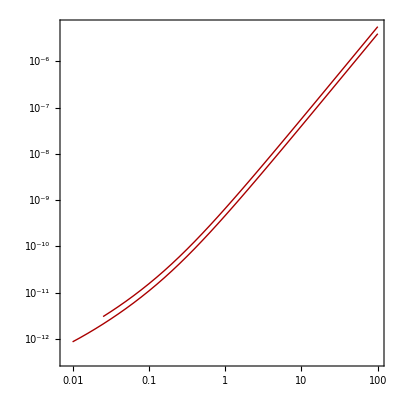

```mathematica
pλξ=ListLogLogPlot[{data50[[All,{1,2}]],data60[[All,{1,2}]]},
AspectRatio->1,
Frame->True,
Joined->True,
 PlotStyle->{{Darker[Red],Thick},{Darker[Red],Thin}},
FrameStyle->BlackFrame
,BaseStyle->texStyle,
FrameTicks->{{All ,Automatic},{All,Automatic}}
,
FrameStyle->Directive[Thickness[0.002],FontSize->24,Black],
FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"\\xi","\\lambda_\\sigma"}
]
```

```mathematica
Export[NotebookDirectory[] <>"plotlambdaxi2.pdf", pλξ, "PDF"]
```

/Users/sofiane/Dropbox/Physics/papers_finished/1712.06526_SU5U1/mate/plotlambdaxi2.pdf

## >> r vs ξ

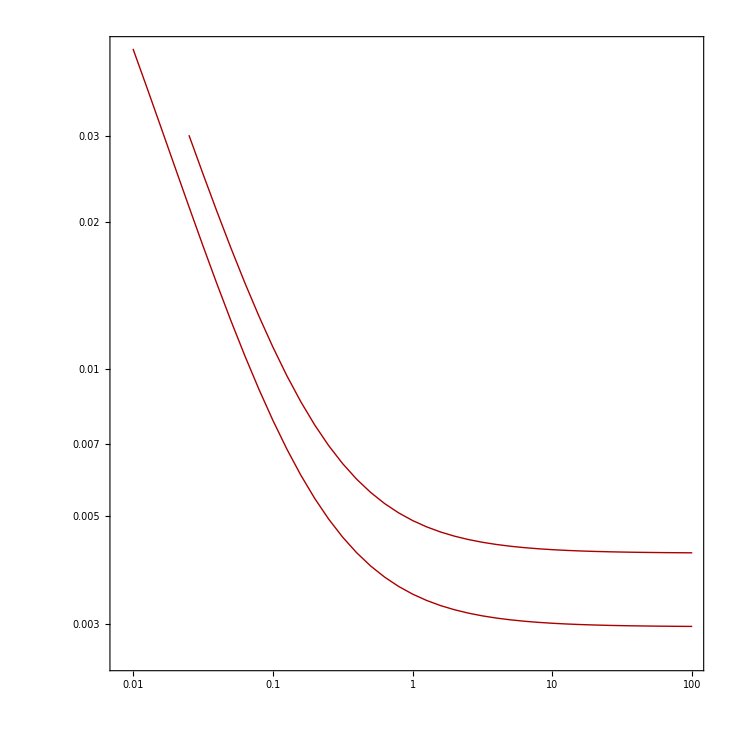

```mathematica
prξ=ListLogLogPlot[{data50[[All,{1,4}]],data60[[All,{1,4}]]},
AspectRatio->1,
Frame->True,
Joined->True,
GridLines->{None,None},
 PlotStyle->{{Darker[Red],Thick},{Darker[Red],Thin}},
FrameStyle->BlackFrame,
(*FrameTicks->{{Table[{10^x,MaTeX[x,Magnification->1.3]},{x, Range[-12,5]}],None},{Table[{10^x,MaTeX[x,Magnification->1.3]},{x, Range[-2,3]}],None}},*)
BaseStyle->texStyle,
FrameStyle->Directive[Thickness[0.002],FontSize->24,Black],
FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"\\xi","r"}
]
```

## >> r vs ns

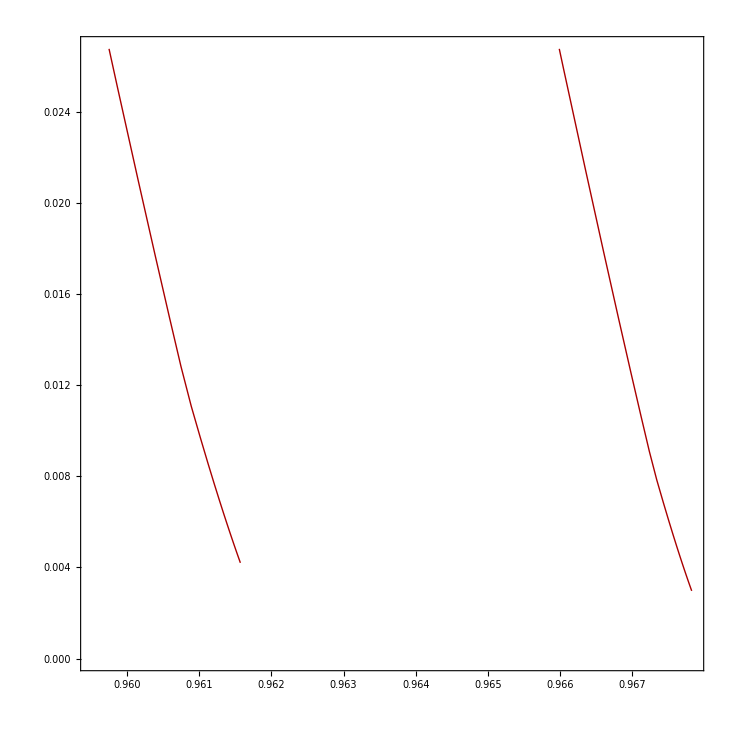

```mathematica
pλξ=ListPlot[{data50[[All,{3,4}]],data60[[All,{3,4}]]},
AspectRatio->1,
Frame->True,
Joined->True,
GridLines->{None,None},
 PlotStyle->{{Darker[Red],Thick},{Darker[Red],Thin}},
FrameStyle->BlackFrame,
(*FrameTicks->{{Table[{10^x,MaTeX[x,Magnification->1.3]},{x, Range[-12,5]}],None},{Table[{10^x,MaTeX[x,Magnification->1.3]},{x, Range[-2,3]}],None}},*)
BaseStyle->texStyle,
FrameStyle->Directive[Thickness[0.002],FontSize->24,Black],
FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"n_s","r"}
]
```

```mathematica
Export[NotebookDirectory[] <>"plotlambdaxi2.pdf", pλξ, "PDF"]
```

/Users/sofiane/Dropbox/Physics/papers_finished/1712.06526_SU5U1/mate/plotlambdaxi2.pdf

## >> α vs ξ

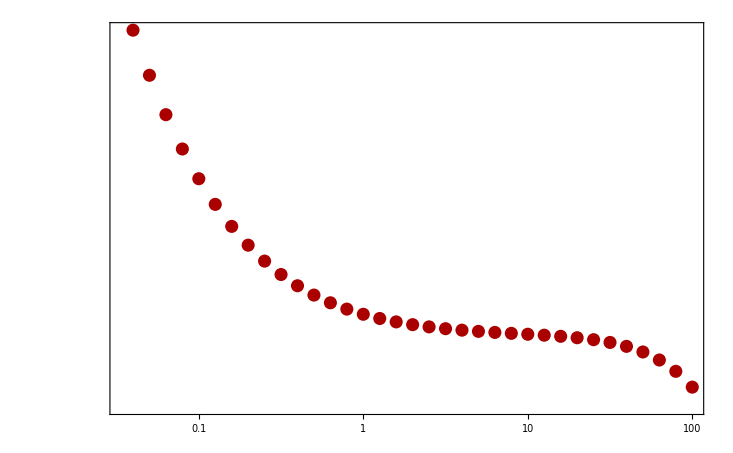

```mathematica
dataξvsα good=Abs[data50[[All,{1,5}]]];

plotλξα=ListLogLogPlot[Abs[data50[[All,{1,5}]]],
Frame->True,
Joined->False,
GridLines->{None,None},
 PlotStyle->{Darker[Red],Thick},
FrameStyle->BlackFrame,
(*FrameTicks->{{Table[{10^x,MaTeX[x,Magnification->1.3]},{x, Range[-12,5]}],None},{Table[{10^x,MaTeX[x,Magnification->1.3]},{x, Range[-2,3]}],None}},*)
BaseStyle->texStyle,
FrameStyle->Directive[Thickness[0.002],FontSize->24,Black],
FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{log}_{10}\\xi","-10^{-4}\\alpha"}
]
```

## >> H vs ξ

```mathematica
dataξvsH good=dataInf good[[All,{1,6}]];
```

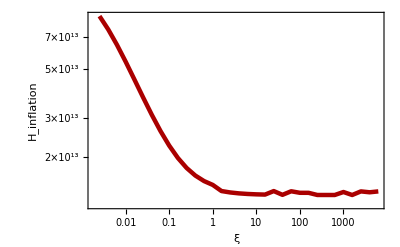

```mathematica
plotHξ=ListLogLogPlot[dataξvsH good,Frame->True,Joined->True,GridLines->{Automatic,Automatic}, PlotStyle->{Darker[Red],Thickness[0.008]},GridLinesStyle->Thin, FrameStyle->Directive[Black,Thickness[0.006]],
FrameLabel->{"ξ","H_inflation"},LabelStyle->Directive[FontFamily->"Helvetica",Black,30,Bold]
]
```

## >> κ vs ξ

```mathematica
10^13. 70^2
```

4.9×10^16

```mathematica
Clear[ϕ init,ξind,MGUT GeV]
```

```mathematica
Solve[((1/((ξ ρ^2 )^2)(MGUT^2))/((10^13.)^2)==1),MGUT]//Simplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{MGUT→-1.×10^13 ξ ρ^2},{MGUT→1.×10^13 ξ ρ^2}}

```mathematica
((1/((ξ ρ^2 )^2)(MGUT^2-Abs[κ]  ρ^2 Mpl^2))/(Hinf^2/(4 π^2)))/.{Hinf->6.3347093986338914*^13,Mpl->Mpl GeV,ξ->0.01,ρ->20,MGUT->MGUT GeV}/.κ->0.2 1.5116221131501728*^-8
```

17708.6

```mathematica
{1/((ξ ρ^2 )^2)(MGUT^2) , Hinf^2/(4 π^2),(4 MGUT^2-(Hinf^2 ξ^2 ρ^4)/π^2)/(4 Mpl^2 ρ^2)}/.{Hinf->6.3347093986338914*^13,Mpl->Mpl GeV,ξ->0.01,ρ->20,MGUT->MGUT GeV}//N
```

{2.25×10^30,1.01647×10^26,1.51162×10^-8}

```mathematica
{√(1/((ξ ρ^2 )^2)(MGUT^2+Abs[κ]  ρ^2 Mpl^2)) ,√(Hinf^2/(4 π^2))}/.{Hinf->6.3347093986338914*^13,Mpl->Mpl GeV,ξ->0.01,ρ->20,MGUT->MGUT GeV}/.κ->1.5116221131501725*^-8//N
```

{2.1213×10^15,1.0082×10^13}

```mathematica
dataκ={};dataκOK={}; MGUT GeV=6 10^15.;(*6.7 10^15;*)
For[ξind=-2.,ξind≤2.,ξind+=.2,
sol=Nk Above[10^ξind,False];
ϕ init=sol[[1]];
V0=sol[[2]];
λ=sol[[3]];

(*low=(1+10^ξind (ϕ init)^2)(Hinflation[ϕ init,10^ξind,V0,λ]/(2π ϕ init  Mpl GeV))^2+(MGUT GeV)/(ϕ init  Mpl GeV);*)
low=(4 MGUT^2-(Hinf^2 ξ^2 ρ^4)/π^2)/(4 (Mpl GeV)^2 ρ^2)/.{ξ->10.^ξind,ρ->ϕ init,MGUT->MGUT GeV,Hinf->Hinflation[ϕ init,10^ξind,V0,λ]};
TH=1/((1+10^ξind (ϕ init)^2 )^2)(MGUT GeV^2);

low2=(10.^ξind ϕ init)^2(Hinflation[ϕ init,10^ξind,V0,λ]^2)/(4 π^2 (Mpl GeV)^2);
up=√λ;

(*dataκ=Append[dataκ,{ξind,Log[10,low],Log[10,up]}];*)

dataκ=Append[dataκ,{10^ξind,10^ξind (ϕ init)^2,low,low2,Hinflation[ϕ init,10^ξind,V0,λ],√TH}];

If[low<up,dataκOK=Append[dataκOK,{10^ξind,low,up}]]
];
```

```mathematica
dataκ//TableForm
```

0.01 | 3.9597 | 1.52701×10^-8 | 6.76046×10^-13 | 6.33471×10^13 | 1.20975×10^15
0.0158489 | 6.09438 | 1.5724×10^-8 | 1.1501×10^-12 | 5.29021×10^13 | 8.4574×10^14
0.0251189 | 9.21888 | 1.64738×10^-8 | 1.90978×10^-12 | 4.40274×10^13 | 5.87149×10^14
0.0398107 | 13.6048 | 1.76911×10^-8 | 3.11892×10^-12 | 3.67897×10^13 | 4.10824×10^14
0.0630957 | 19.4157 | 1.96453×10^-8 | 5.03777×10^-12 | 3.10894×10^13 | 2.93891×10^14
0.1 | 26.5622 | 2.27565×10^-8 | 8.07733×10^-12 | 2.67345×10^13 | 2.1769×10^14
0.158489 | 34.6 | 2.7685×10^-8 | 1.28839×10^-11 | 2.34993×10^13 | 1.68539×10^14
0.251189 | 42.7397 | 3.55174×10^-8 | 2.04979×10^-11 | 2.11841×10^13 | 1.37175×10^14
0.398107 | 50.1729 | 4.79467×10^-8 | 3.25619×10^-11 | 1.95745×10^13 | 1.17249×10^14
0.630957 | 56.348 | 6.76569×10^-8 | 5.16793×10^-11 | 1.84837×10^13 | 1.04624×10^14
1. | 61.0875 | 9.89033×10^-8 | 8.19762×10^-11 | 1.77598×10^13 | 9.66378×10^13
1.58489 | 67.4038 | 1.42056×10^-7 | 1.24417×10^-10 | 1.6545×10^13 | 8.77144×10^13
2.51189 | 69.6096 | 2.18002×10^-7 | 1.9799×10^-10 | 1.63139×10^13 | 8.49743×10^13
3.98107 | 71.0857 | 3.38327×10^-7 | 3.14602×10^-10 | 1.61644×10^13 | 8.32342×10^13
6.30957 | 72.0533 | 5.29004×10^-7 | 4.99424×10^-10 | 1.60686×10^13 | 8.21319×10^13
10. | 72.6788 | 8.31192×10^-7 | 7.9235×10^-10 | 1.60075×10^13 | 8.14346×10^13
15.8489 | 73.0797 | 1.31012×10^-6 | 1.25661×10^-9 | 1.59688×10^13 | 8.09939×10^13
25.1189 | 70.0746 | 2.16543×10^-6 | 2.0851×10^-9 | 1.6686×10^13 | 8.44184×10^13
39.8107 | 73.4973 | 3.27214×10^-6 | 3.15857×10^-9 | 1.59287×10^13 | 8.05398×10^13
63.0957 | 70.36 | 5.41723×10^-6 | 5.23737×10^-9 | 1.66519×10^13 | 8.40807×10^13
100. | 71.7412 | 8.42042×10^-6 | 8.1489×10^-9 | 1.63394×10^13 | 8.24842×10^13

```mathematica
10^13*70.
```

7.×10^14

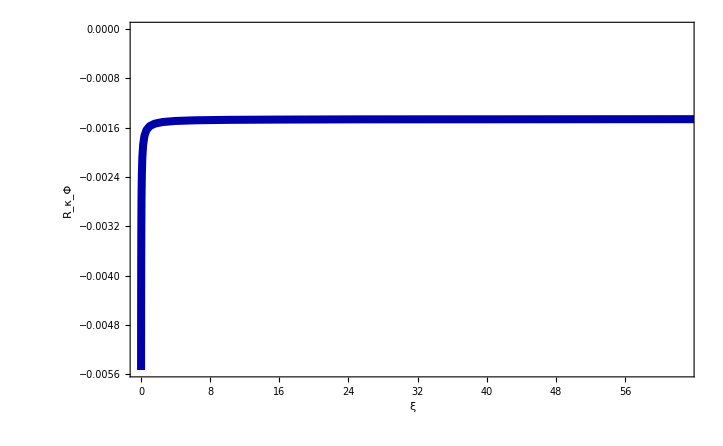

```mathematica
plotκξ=ListPlot[
dataκ,
Frame->True,
Joined->True,
GridLines->{None,None},
GridLinesStyle->None,
 Filling->{3->{4}},
FillingStyle->Lighter[LightRed], PlotStyle->{Darker[Blue],Thickness[0.008]},
 FrameStyle->Directive[Black,Thickness[0.006]],
FrameLabel->{"ξ","R_κ_Φ"},
 LabelStyle->Directive[FontFamily->"Helvetica",Black,60,Bold]
]
```

```mathematica
Export[NotebookDirectory[] <>"plotkappaxi.pdf", plotκξ, "PDF", "CompressionLevel"->0,ImageSize-> 2000,ImageResolution->300]
```

/Users/sofiane/Dropbox/projects/SU5U1/mate/plotkappaxi.pdf

## >> y vs ξ

```mathematica
β[λ_,y_]:=1/(16 π^2)(20 λ^2+2 3λ(y^2)-3 y^4)
β2[λ_,y_]:=1/(16 π^2)(-3 y^4)
```

```mathematica
sols2=Solve[Abs[β2[λ,y]]==(λ/4),y]
```

{{y→-(√(2 π) λ^(1/4))/3^(1/4)},{y→-(ⅈ √(2 π) λ^(1/4))/3^(1/4)},{y→(ⅈ √(2 π) λ^(1/4))/3^(1/4)},{y→(√(2 π) λ^(1/4))/3^(1/4)}}

```mathematica
y2[λs_]:=sols2[[4,1,2]]/.λ->λs
```

```mathematica
y2[0.01]
```

0.602296

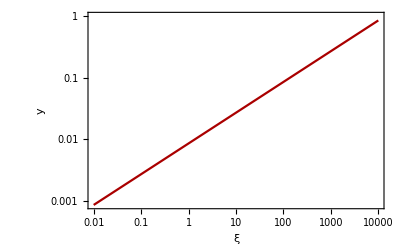

```mathematica
plotyξ=LogLogPlot[{y2[fλvsξ[ξ]]},{ξ,0.01,10^4},Frame->True,PlotStyle->{{Darker[Red]},{Darker[Red],Thickness[0.007]}},
FrameLabel->{"ξ","y"},LabelStyle->Directive[FontFamily->"Helvetica",40,Bold]]
```

```mathematica
y3[λ_]:=2 √λ
```

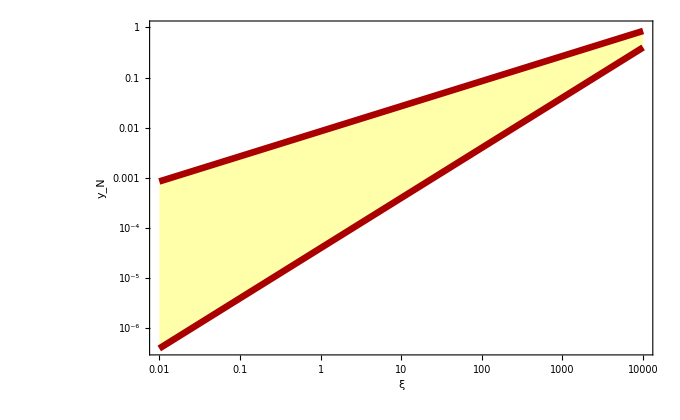

```mathematica
plotyξ=LogLogPlot[{y3[fλvsξ[ξ]],y2[fλvsξ[ξ]]},{ξ,0.01,10^4},Frame->True,Frame->True,Filling->{1->{2}},FillingStyle->Directive[Lighter[Yellow],Opacity[0.5]],GridLinesStyle->Thick, FrameStyle->Directive[Black,Thickness[0.006]],GridLines->Automatic,PlotStyle->{{Darker[Red],Thickness[0.007]},{Darker[Red],Thickness[0.007]},{Darker[Gray],Dashed}},
FrameLabel->{"ξ","y_N"},LabelStyle->Directive[FontFamily->"Helvetica",60,Bold]]
```

```mathematica
Export[NotebookDirectory[] <>"plotyxi.pdf", plotyξ, "PDF", "CompressionLevel"->0,ImageSize-> 2000,ImageResolution->300]
```

/Users/sofiane/Dropbox/projects/SU5U1/mate/plotyxi.pdf

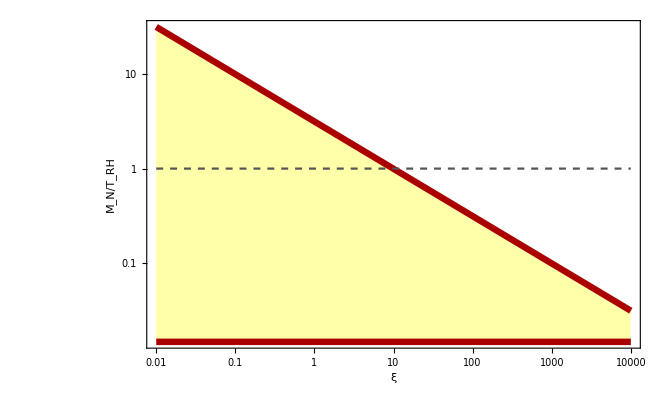

```mathematica
plotMNTRξ=LogLogPlot[{(y3[fλvsξ[ξ]]10^12/√2)/(9.584146563694086*^13 √fλvsξ[ξ]),(y2[fλvsξ[ξ]]10^12/√2)/(9.584146563694086*^13 √fλvsξ[ξ]),1},{ξ,0.01,10^4},Frame->True,Filling->{1->{2}},FillingStyle->Directive[Lighter[Yellow],Opacity[0.5]],GridLinesStyle->Thick, FrameStyle->Directive[Black,Thickness[0.006]],GridLines->Automatic,PlotStyle->{{Darker[Red],Thickness[0.007]},{Darker[Red],Thickness[0.007]},{Darker[Gray],Dashed}},
FrameLabel->{"ξ","M_N/T_RH"},LabelStyle->Directive[FontFamily->"Helvetica",Black,60,Bold]]
```

```mathematica
Export[NotebookDirectory[] <>"plotmntrxi.pdf", plotMNTRξ, "PDF", "CompressionLevel"->0,ImageSize-> 2000,ImageResolution->300]
```

/Users/sofiane/Dropbox/projects/SU5U1/mate/plotmntrxi.pdf

```mathematica
4*16
```

64

## > Reheat

```mathematica
0.1 √((3λs)/(64π)(√(2λs) faa) MPL GeV)/.{faa-> 10^12,λs->10^-8}
```

5.03204×10^7

```mathematica
0.1 √(λ^2/(32π)faa^2/mρ MPL GeV)/.mρ->√(2λ) faa/.yN->√λ(*√(2π)(λ/3)^(1/4)*)/.faa-> 10^14/.λ->10^-7
```

1.63374×10^9

```mathematica
(32.π mρ)/faa/.mρ->√(2λ) faa/.yN->√λ(*√(2π)(λ/3)^(1/4)*)/.faa-> 10^14/.λ->10^-7
```

0.0449588

```mathematica
Solve[ΩDMa[5 10^11,θ2]==0.119,θ2]
```

{{θ2→0.625201}}

```mathematica
Solve[(yN faa /√2==0.1 √((3yN^2)/(64π)mρ MPL GeV))/.mρ->√(2λ) faa/.yN->√λ,faa]/.λ->10^-8
```

{{faa→0.},{faa→5.06428×10^11}}

## > Isocurvatures

```mathematica
iso EXP=0.038; (* PLANCK 1502.02114*)
OmegaDM EXP=0.119; (* PLANCK 1502.02114*)
```

```mathematica
ΩDMa[fa_,θ2_]:=OmegaDM EXP(θ2/(6 10^-6)) (fa/10^16)^(7/6);

αISO[θ2_,ξ_,ρ_]:=1/(1+(π ρ^2 θ2)/ϵ[ρ,ξ,0]);
```

```mathematica
dataρξ50=Drop[data50[[All,{1,7}]],1];
dataρξ60=Drop[data60[[All,{1,7}]],1];
```

```mathematica
dataIso50=Table[{dataρξ50[[i,1]],
θ2sol=Solve[{αISO[θ2,dataρξ50[[i,1]],dataρξ50[[i,2]]]==iso EXP},θ2][[1,1,2]],
Solve[ΩDMa[faa,θ2sol]==0.119,faa][[1,1,2]]},
{i,1,Length[dataρξ50]}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
dataIso60=Table[{dataρξ60[[i,1]],
θ2sol=Solve[{αISO[θ2,dataρξ60[[i,1]],dataρξ60[[i,2]]]==iso EXP},θ2][[1,1,2]],
Solve[ΩDMa[faa,θ2sol]==0.119,faa][[1,1,2]]},
{i,1,Length[dataρξ60]}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

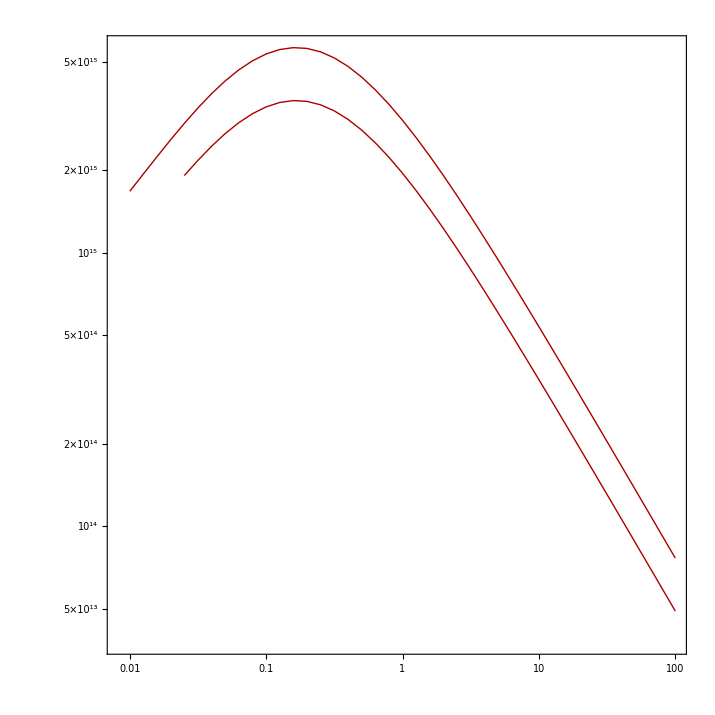

```mathematica
pFaξ=ListLogLogPlot[{dataIso50[[All,{1,3}]],dataIso60[[All,{1,3}]]},
AspectRatio->1,
Frame->True,
Joined->True,
GridLines->{None,None},
 PlotStyle->{{Darker[Red],Thick},{Darker[Red],Thin}},
FrameStyle->BlackFrame,
(*FrameTicks->{{Table[{10^x,MaTeX[x,Magnification->1.3]},{x, Range[13.0,15.2,0.2]}],None},{Table[{10^x,MaTeX[x,Magnification->1.3]},{x, Range[-2,3]}],None}},*)
BaseStyle->texStyle,
FrameStyle->Directive[Thickness[0.002],FontSize->24,Black],
FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"\\xi","f_a"}
]
```

```mathematica
Export[NotebookDirectory[] <>"plotfaxi2.pdf", pFaξ, "PDF"]
```

/Users/sofiane/Dropbox/Physics/papers_finished/1712.06526_SU5U1/mate/plotfaxi2.pdf

## > Cosmological Constant

```mathematica
Clear[fa]
```

```mathematica
Limit[ΔR2[ϕ,λ,0,ξ,0]/.fa->0,ξ->0]//FullSimplify
```

(λ ϕ^6)/(768 π^2)

```mathematica
rvbl=Quiet[FindRoot[(D[V[Φ,0,1,0],Φ]/.Φ->ϕ)==0.,{ϕ,1}][[1,2]]]
```

8.26743×10^7

```mathematica
rv0=-V[rvbl,0,ξ,0]
```

-(1.16794×10^31)/((1+6.83504×10^15 ξ)^2)

```mathematica
λforξ[ξ_,ϕinf_]:=Block[{ϕmin,CC},
fa=10^11/MPL GeV;
ϕmin=Quiet[FindRoot[(D[V[Φ,0,ξ,0],Φ]/.Φ->ϕ)==0.,{ϕ,1}][[1,2]]];
CC=-V[ϕmin,0,ξ,0];
FindRoot[ΔR2[ϕinf,λ,0,ξ,CC]==2.215 10^-9,{λ,10^-2}][[1,2]]

]
```